# Analysis of axisymmetric necking using the one-dimensional model of Yu and Fu (2024)

This Mathematica code produces the results presented in Section 5 of Yu  and Fu (2024).  It is a simplified version for a quick presentation of the main idea.
It takes about 10 minutes to run this code on an Apple M2 Pro processor.

Note: Due to the existence of turning points in the loading curve,  we had to compute the growth stage and propagation stage of axisymmetric necking separately .

```mathematica
Clear["`*"](*Clear all variables*)
```

```mathematica
starttime= DateList[]
```

{2024,12,1,10,24,19.893145}

## 1. Growth stage of necking

#### 1. 1d energy functional, and interpolation using linear functions

```mathematica
ρ=μ^-1 λ^-1;
int=(w[ρ,μ]+N[1/24] H^2 w1[ρ,μ]/ρ λp^2-𝓆(μ+R μp-ρ))R;(*Integrand of the 1d energy functional given in eqn (5.12), μp=μ'[R], λp=λ'[R]. For the electroelastic case, modify this integrand to account for the contribution of the applied voltage*)
sublinear={μ->N[(1-ξ)] μ[j]+N[ξ] μ[1+j],μp->1/h(-μ[j]+μ[1+j]),λ->N[(1-ξ)] λ[j]+N[ξ] λ[1+j],λp->1/h(-λ[j]+λ[1+j]),𝓆->N[(1-ξ)] q[j]+N[ξ]q[1+j],R->h j+h ξ}; (*Linear interpolation rule*)
{ξ1,ξ2}={1/2(1-1/(√3)),1/2(1+1/(√3))}//N;(*Gaussian points of the interval [0,1]*)
{g1,g2}={1/2,1/2}//N;(*Gaussian weights*)
sub1=sublinear/.{ξ->ξ1};
sub2=sublinear/.{ξ->ξ2};
```

#### 2. Geometry and material parameters, and strain energy function

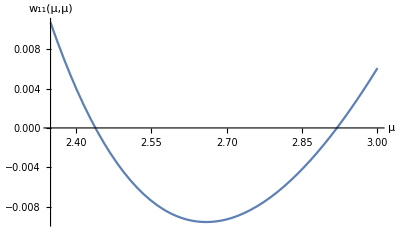

{2.43918,0.168078,1.97955}

```mathematica
H=N[2];(* Initial thickness*)
A=N[10];(*Initial radius*)
w[x_,y_]=N[(2 μ1)/m1^2](x^m1+y^m1+x^-m1 y^-m1-3.)+N[(2 μ2)/m2^2](x^m2+y^m2+x^-m2 y^-m2-3.)/.{μ1->N[1],m1->N[1/2],μ2->N[1/80],m2->N[4]};(*Strain energy function defined in eqn (5.16)*)
w1[x_,y_]=D[w[x,y],x];
w11[x_,y_]=D[w[x,y],{x,2}];
Plot[w11[x,x],{x,2.35,3},AxesLabel->{HoldForm[μ],HoldForm[Subscript[w, 11][μ,μ]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]}](*Plot the graph of Subscript[w, 11](μ,μ) as a fucntion of μ*)
μcr=x/.FindRoot[w11[x,x]==0,{x,2}];(*Find critical value of μ, see eqn (5.6)*)
λcr=μcr^-2;
Pcr=w1[μcr,μcr];
bifpt={μcr,λcr,Pcr} (*Bifurcation point*)
```

#### 3. Discretization of the 1d energy functional, and its stationary conditions

```mathematica
n=400; (*Number of mesh points, can be increased for more accurate results*)
h=N[A/n];(*Mesh size*)
DateList[]
ℰ1d=Sum[g1(int/.sub1)+g2(int/.sub2),{j,0,n-1}]; (*Discretization of the integral given in eqn (5.12*)
eqμ0=μ[0]-μ0; (*μ0 is used as the control parameter*)
eqμ=Table[D[ℰ1d,μ[j]],{j,0,n-1}];
eqλ=Table[D[ℰ1d,λ[j]],{j,0,n}];
eqq=Table[D[ℰ1d,q[j]],{j,0,n}];
eqs=Join[{eqμ0==0},Table[eqμ[[j]]==0,{j,1,Length[eqμ]}],Table[eqλ[[j]]==0,{j,1,Length[eqλ]}],Table[eqq[[j]]==0,{j,1,Length[eqq]}]];(*3n+3 algebraric equations given by eqn (5.15)*)
DateList[]
P=h/A^2 D[ℰ1d,μ[n]];(*The tensile force at the edge*)
eqs//Length
```

{2024,12,1,10,24,20.025934}

{2024,12,1,10,24,33.635903}

1203

#### 4. Solving the system of algebraic equations near the bifurcation point, starting from μ0=μ0st=2.45

```mathematica
μ0st=2.45;(*The critical value of μ is Subscript[μ, cr]=2.439*)
μ0=μ0st;
yintp=InterpolatingFunction[…];(* "yintp" refers to the leading-order solution Subscript[y, 1][X] in the weakly nonlinear analysis, see eqn (5.9). It is computed using the finite difference scheme detailed in Fu and Yu, Mech. Mater. 2023*)
zintp=InterpolatingFunction[…];(* "zintp" refers to -2Subscript[y, 1][X}+R Subscript[y, 1]'[x]*)
μ∞=(-μ0+μcr yintp[0])/(-1+yintp[0]);(*"μ∞" refers to "a" in the paper*)
μw[R_]=μ∞+(μcr-μ∞)yintp[√(μcr-μ∞)R]; (* Weakly nonlinear solution of μ[R], see eqn (5.8)*)
λw[R_]=1/(μ∞)^2+((μcr-μ∞)zintp[√(μcr-μ∞)R])/(μ∞)^3;
qw[R_]=-Derivative[1,0][w][μcr,μcr]-(μcr-μ∞) (-1+yintp[√(μcr-μ∞)R]) Derivative[1,1][w][μcr,μcr];
guess=Join[Table[{μ[j],μw[j h]},{j,0,n}],Table[{λ[j],λw[ j h]},{j,0,n}],Table[{q[j],qw[j h]},{j,0,n}]];(*Use the weakly nonlinear solution as initial guess*)
guess//Length
DateList[]
solsub=FindRoot[eqs,guess];(*Find the solution using the Newton-Raphson method*)
DateList[]
```

1203

{2024,12,1,10,24,33.699332}

{2024,12,1,10,24,40.037573}

#### 5. Plot the graph of the 1d solution obtained above

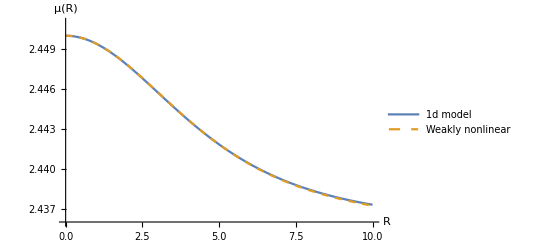

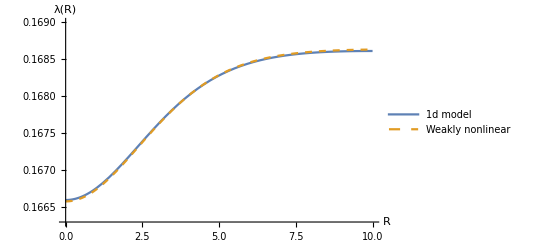

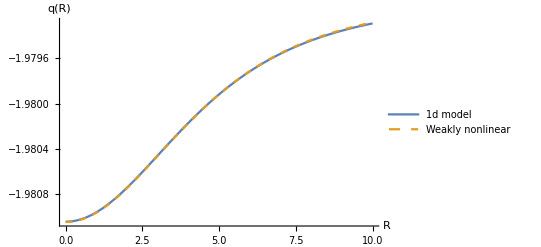

```mathematica
μ1d[R_]=Piecewise[Table[{((h+h j-R) μ[j]+(-h j+R) μ[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
λ1d[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
q1d[R_]=Piecewise[Table[{((h+h j-R) q[j]+(-h j+R) q[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
Plot[{μ1d[R],μw[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.8}],AxesLabel->{HoldForm[R],HoldForm[μ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{0,10},{2.436,2.451}}]
Plot[{λ1d[R],λw[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.3}],AxesLabel->{HoldForm[R],HoldForm[λ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{0,10},{0.1663,0.169}}]
Plot[{q1d[R],qw[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.3}],AxesLabel->{HoldForm[R],HoldForm[q[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->Full]
dataload={{μ0,μ[0],μ[n],λ[0],λ[n],P}}/.solsub;
datasol={solsub};  (*Collect data*)
```

#### 6. Continue the solution to the fully nonlinear regime using a do-loop, using the solution at the previous step as the guess for the current step

```mathematica
kmax=32;(*Maximum iteration step*)
startime=DateList[]
Do[μ0=μ0st+k*0.06;
guess=Join[Table[{μ[j],μ[j]/.solsub},{j,0,n}],Table[{λ[j],λ[j]/.solsub},{j,0,n}],Table[{q[j],q[j]/.solsub},{j,0,n}]];
solsub=FindRoot[eqs,guess];
dataload=Append[dataload,{μ0,μ[0],μ[n],λ[0],λ[n],P}/.solsub];
datasol=Append[datasol,solsub];
Print[{k,μ0,μ[0],μ[n]}/.solsub],{k,1,kmax}];
endtime=DateList[]
```

{2024,12,1,10,24,40.680301}

{1,2.51,2.51,2.41716}

{2,2.57,2.57,2.3996}

{3,2.63,2.63,2.38396}

{4,2.69,2.69,2.36989}

{5,2.75,2.75,2.35713}

{6,2.81,2.81,2.34546}

{7,2.87,2.87,2.33471}

{8,2.93,2.93,2.32471}

{9,2.99,2.99,2.31533}

{10,3.05,3.05,2.30644}

{11,3.11,3.11,2.29789}

{12,3.17,3.17,2.28954}

{13,3.23,3.23,2.28122}

{14,3.29,3.29,2.27271}

{15,3.35,3.35,2.26371}

{16,3.41,3.41,2.25377}

{17,3.47,3.47,2.2422}

{18,3.53,3.53,2.22808}

{19,3.59,3.59,2.21108}

{20,3.65,3.65,2.19289}

{21,3.71,3.71,2.17672}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{22,3.77,3.73914,2.17259}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{23,3.83,3.75516,2.17253}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{24,3.89,3.76608,2.1746}

{25,3.95,3.77395,2.17799}

{26,4.01,3.77961,2.18212}

{27,4.07,3.78394,2.1866}

{28,4.13,3.78759,2.19154}

{29,4.19,3.79026,2.19644}

{30,4.25,3.79266,2.20131}

{31,4.31,3.79471,2.20648}

{32,4.37,3.79665,2.21152}

{2024,12,1,10,29,40.282478}

#### 7. Output the results calculated above

```mathematica
kend=21 (*The numerical continuation fails to converge at k=21, since μ[0] almost attains its maximum at this step and  can not be increased further.*)
datasol(* "datasol" consists of all solution calculated in the iteration procedure*)
dataAmp=Join[{{μcr,0}},Table[{μ[n],λ[n]-λ[0]}/.datasol[[i]],{i,1,Length[datasol]}]] (* λ[A]-λ[0] versus μ[0]*)
dataμ0=Join[{{μcr,μcr}},Table[{μ[n],μ[0]}/.datasol[[i]],{i,1,Length[datasol]}]]  (* μ[0] versus μ[n]*)
```

21

{{μ[0]→2.45,μ[1]→2.45,μ[2]→2.45,μ[3]→2.45,μ[4]→2.44999,μ[5]→2.44999,μ[6]→2.44998,μ[7]→2.44998,μ[8]→2.44997,μ[9]→2.44997,μ[10]→2.44996,μ[11]→2.44995,μ[12]→2.44994,μ[13]→2.44993,μ[14]→2.44992,1173,q[386]→-1.97931,q[387]→-1.97931,q[388]→-1.97931,q[389]→-1.97931,q[390]→-1.97931,q[391]→-1.9793,q[392]→-1.9793,q[393]→-1.9793,q[394]→-1.9793,q[395]→-1.9793,q[396]→-1.9793,q[397]→-1.9793,q[398]→-1.97929,q[399]→-1.97929,q[400]→-1.97929},31,{1}}
 |  |  |  |

{{2.43918,0},{2.4373,0.00201622},{2.41716,0.0126903},{2.3996,0.0225309},{2.38396,0.0316513},{2.36989,0.0401302},{2.35713,0.0480353},{2.34546,0.0554255},{2.33471,0.0623529},{2.32471,0.0688647},{2.31533,0.0750046},{2.30644,0.0808138},{2.29789,0.0863329},{2.28954,0.0916032},{2.28122,0.0966699},{2.27271,0.101586},{2.26371,0.106421},{2.25377,0.111273},{2.2422,0.116291},{2.22808,0.121685},{2.21108,0.127599},{2.19289,0.133858},{2.17672,0.140231},{2.17259,0.143163},{2.17253,0.14483},{2.1746,0.146007},{2.17799,0.146842},{2.18212,0.147466},{2.1866,0.147943},{2.19154,0.148337},{2.19644,0.14865},{2.20131,0.148906},{2.20648,0.149137},{2.21152,0.149328}}

{{2.43918,2.43918},{2.4373,2.45},{2.41716,2.51},{2.3996,2.57},{2.38396,2.63},{2.36989,2.69},{2.35713,2.75},{2.34546,2.81},{2.33471,2.87},{2.32471,2.93},{2.31533,2.99},{2.30644,3.05},{2.29789,3.11},{2.28954,3.17},{2.28122,3.23},{2.27271,3.29},{2.26371,3.35},{2.25377,3.41},{2.2422,3.47},{2.22808,3.53},{2.21108,3.59},{2.19289,3.65},{2.17672,3.71},{2.17259,3.73914},{2.17253,3.75516},{2.1746,3.76608},{2.17799,3.77395},{2.18212,3.77961},{2.1866,3.78394},{2.19154,3.78759},{2.19644,3.79026},{2.20131,3.79266},{2.20648,3.79471},{2.21152,3.79665}}

#### 8. Loading curves (bifurcation diagrams) corresponding to the stage of necking growth

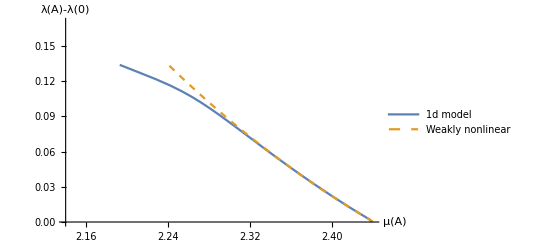

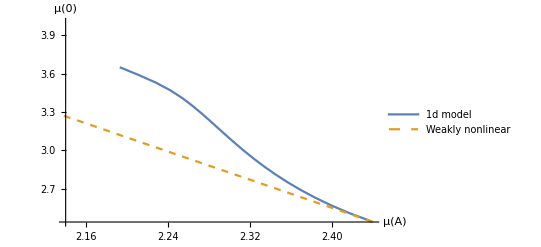

```mathematica
Clear[μ∞]
μ∞=(x-yintp[0] μcr)/(1-yintp[0]);(*“x” stands for “μ0”. Given μ0, μ∞ is determiend from μ[R]=μ∞+(μcr-μ∞)yintp[√(μcr-μ∞)A]*)
dataAmpw=Table[{μ∞+(μcr-μ∞)yintp[√(μcr-μ∞)A],((μcr-μ∞)zintp[√(μcr-μ∞)A])/(μ∞)^3-((μcr-μ∞)zintp[0])/(μ∞)^3},{x,μcr,3,0.004}];(* λ[A]-λ[n] versus μ[n] given by weakly nonlinear analysis*)
dataμ0w=Table[{μ∞+(μcr-μ∞)yintp[√(μcr-μ∞)A],x},{x,μcr,3.5,0.004}];(* μ[0] versus μ[n] given by weakly nonlinear analysis*)
ListPlot[{dataAmp[[1;;kend+1]],dataAmpw},Joined->True,AxesLabel->{HoldForm[μ[A]],HoldForm[λ[A]-λ[0]]},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.3,0.2}],LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{2.14,2.44},{0,0.17}}]
ListPlot[{dataμ0[[1;;kend+1]],dataμ0w},Joined->True,AxesLabel->{HoldForm[μ[A]],HoldForm[μ[0]]},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.3,0.2}],LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{2.14,2.44},{2.44,4}}]
```

Observe that λ(A) and λ(0) are the averaged membrane thicknesses at R=A and 0, respectively, where μ is the averaged azimuthal stretch

## 2 Propagation stage of necking

#### 1. Stationary conditions of the discretized 1d energy functional, but now we use μA as the control parameter

```mathematica
Clear[μA,eqs];
eqμA=μ[n]-μA; (* μA is used as the control paramter*)
eqs=Join[Table[eqμ[[j]]==0,{j,1,Length[eqμ]}],{eqμA==0},Table[eqλ[[j]]==0,{j,1,Length[eqλ]}],Table[eqq[[j]]==0,{j,1,Length[eqq]}]];
eqs//Length
```

1203

#### 2. Solving the system of algebraic equations in the propagation stage, starting from μA=μAst=2.19.

```mathematica
μAst=2.19;
μA=μAst;
inisub=datasol[[29]];(*initial guess for the necking in the propgation stage*)
guess=Join[Table[{μ[j],μ[j]/.inisub},{j,0,n}],Table[{λ[j],λ[j]/.inisub},{j,0,n}],Table[{q[j],q[j]/.inisub},{j,0,n}]];
guess//Length
DateList[]
solsub=FindRoot[eqs,guess];
DateList[]
```

1203

{2024,12,1,10,29,41.128742}

{2024,12,1,10,29,47.633852}

#### 3. Plot the graph of the 1d solution obtained above

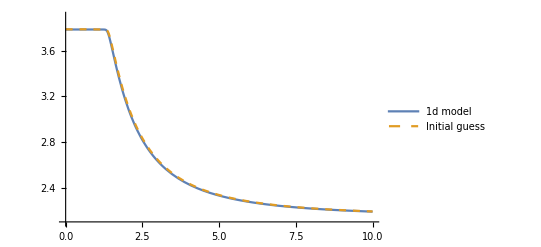

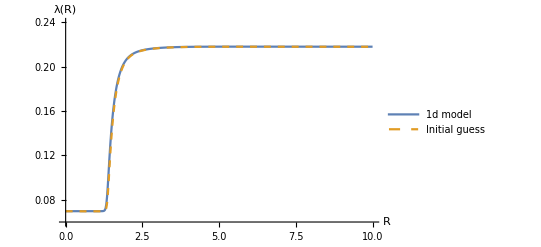

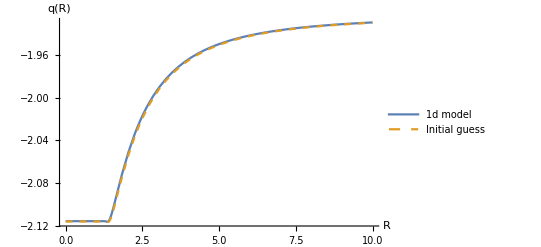

```mathematica
μguess[R_]=Piecewise[Table[{((h+h j-R) μ[j]+(-h j+R) μ[1+j])/h/.inisub,j h<=R<(j+1)h},{j,0,n-1}]];
λguess[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.inisub,j h<=R<(j+1)h},{j,0,n-1}]];
qguess[R_]=Piecewise[Table[{((h+h j-R) q[j]+(-h j+R) q[1+j])/h/.inisub,j h<=R<(j+1)h},{j,0,n-1}]];
μ1d[R_]=Piecewise[Table[{((h+h j-R) μ[j]+(-h j+R) μ[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
λ1d[R_]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
q1d[R_]=Piecewise[Table[{((h+h j-R) q[j]+(-h j+R) q[1+j])/h/.solsub,j h<=R<(j+1)h},{j,0,n-1}]];
Plot[{μ1d[R],μguess[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Initial guess"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.5}],LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{0,10},{2.1,3.9}}]
Plot[{λ1d[R],λguess[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Initial guess"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.4}],AxesLabel->{HoldForm[R],HoldForm[λ[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->{{0,10},{0.06,0.24}}]
Plot[{q1d[R],qguess[R]},{R,0,A},PlotStyle->{Full,Dashed},PlotLegends->Placed[LineLegend[{"1d model","Initial guess"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.5}],AxesLabel->{HoldForm[R],HoldForm[q[R]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotRange->Full]
dataload2={{μA,μ[n],μ[0],λ[0],λ[n],P}}/.solsub;
datasol2={solsub};
```

#### 4. Continue the solution to the fully nonlinear regime using using a do-loop, using the solution at the previous step as the guess for the current step

```mathematica
kmax=40;
startime=DateList[]
Do[μA=μAst+k*0.04;
guess=Join[Table[{μ[j],1.01*μ[j]/.solsub},{j,0,n}],Table[{λ[j],1.01*λ[j]/.solsub},{j,0,n}],Table[{q[j],1.001*q[j]/.solsub},{j,0,n}]];
solsub=FindRoot[eqs,guess];
dataload2=Append[dataload2,{μA,μ[n],μ[0],λ[0],λ[n],P}/.solsub];
datasol2=Append[datasol2,solsub];
Print[{k,μA,μ[n],μ[0]}/.solsub],{k,1,kmax}];
endtime=DateList[]
```

{2024,12,1,10,29,49.109963}

{1,2.23,2.23,3.80052}

{2,2.27,2.27,3.807}

{3,2.31,2.31,3.81089}

{4,2.35,2.35,3.8135}

{5,2.39,2.39,3.81565}

{6,2.43,2.43,3.81711}

{7,2.47,2.47,3.8184}

{8,2.51,2.51,3.81963}

{9,2.55,2.55,3.82061}

{10,2.59,2.59,3.82134}

{11,2.63,2.63,3.82204}

{12,2.67,2.67,3.82283}

{13,2.71,2.71,3.82346}

{14,2.75,2.75,3.82399}

{15,2.79,2.79,3.82446}

{16,2.83,2.83,3.82483}

{17,2.87,2.87,3.82512}

{18,2.91,2.91,3.82553}

{19,2.95,2.95,3.82605}

{20,2.99,2.99,3.82621}

{21,3.03,3.03,3.82657}

{22,3.07,3.07,3.82689}

{23,3.11,3.11,3.82709}

{24,3.15,3.15,3.8274}

{25,3.19,3.19,3.82765}

{26,3.23,3.23,3.82778}

{27,3.27,3.27,3.82818}

{28,3.31,3.31,3.82822}

{29,3.35,3.35,3.82842}

{30,3.39,3.39,3.82876}

{31,3.43,3.43,3.82885}

{32,3.47,3.47,3.8289}

{33,3.51,3.51,3.82914}

{34,3.55,3.55,3.82938}

{35,3.59,3.59,3.82941}

{36,3.63,3.63,3.82899}

{37,3.67,3.67,3.82709}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{38,3.71,3.71,3.80308}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{39,3.75,3.75,3.84344}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{40,3.79,3.7894,3.85024}

{2024,12,1,10,34,36.518305}

#### 5. Output the results calculated in above

```mathematica
kend2=37 (*The numerical continuation fails to converge at k=37, where the the necking interface is close to the edge.*)
datasol2(* "datasol" consists of all solution calculated in the iteration procedure*)
dataAmp2=Table[{μ[n],λ[n]-λ[0]}/.datasol2[[i]],{i,1,Length[datasol2]}] (* λ[A]-λ[0] versus μ[0]*)
dataμ02=Table[{μ[n],μ[0]}/.datasol2[[i]],{i,1,Length[datasol2]}](* μ[0] versus μ[n]*)
```

37

{{μ[0]→3.78571,μ[1]→3.78575,μ[2]→3.78574,μ[3]→3.78575,μ[4]→3.78574,μ[5]→3.78575,μ[6]→3.78574,μ[7]→3.78575,μ[8]→3.78574,1185,q[392]→-1.92983,q[393]→-1.9298,q[394]→-1.92976,q[395]→-1.92972,q[396]→-1.92969,q[397]→-1.92965,q[398]→-1.92962,q[399]→-1.92958,q[400]→-1.92955},39,{1}}
 |  |  |  |

{{2.19,0.148341},{2.23,0.14993},{2.27,0.150603},{2.31,0.150979},{2.35,0.151194},{2.39,0.151298},{2.43,0.151318},{2.47,0.151269},{2.51,0.151163},{2.55,0.151008},{2.59,0.150812},{2.63,0.15058},{2.67,0.150319},{2.71,0.150034},{2.75,0.149728},{2.79,0.149406},{2.83,0.149073},{2.87,0.14873},{2.91,0.148381},{2.95,0.148029},{2.99,0.147676},{3.03,0.147324},{3.07,0.146975},{3.11,0.146631},{3.15,0.146294},{3.19,0.145964},{3.23,0.145643},{3.27,0.14533},{3.31,0.145026},{3.35,0.144728},{3.39,0.14443},{3.43,0.144121},{3.47,0.143771},{3.51,0.143324},{3.55,0.142653},{3.59,0.141497},{3.63,0.139282},{3.67,0.134597},{3.71,0.115604},{3.75,0.114867},{3.7894,0.0931223}}

{{2.19,3.78571},{2.23,3.80052},{2.27,3.807},{2.31,3.81089},{2.35,3.8135},{2.39,3.81565},{2.43,3.81711},{2.47,3.8184},{2.51,3.81963},{2.55,3.82061},{2.59,3.82134},{2.63,3.82204},{2.67,3.82283},{2.71,3.82346},{2.75,3.82399},{2.79,3.82446},{2.83,3.82483},{2.87,3.82512},{2.91,3.82553},{2.95,3.82605},{2.99,3.82621},{3.03,3.82657},{3.07,3.82689},{3.11,3.82709},{3.15,3.8274},{3.19,3.82765},{3.23,3.82778},{3.27,3.82818},{3.31,3.82822},{3.35,3.82842},{3.39,3.82876},{3.43,3.82885},{3.47,3.8289},{3.51,3.82914},{3.55,3.82938},{3.59,3.82941},{3.63,3.82899},{3.67,3.82709},{3.71,3.80308},{3.75,3.84344},{3.7894,3.85024}}

#### 7. Loading curves

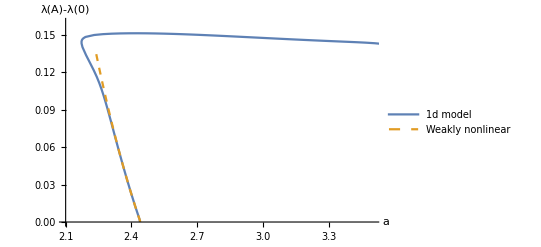

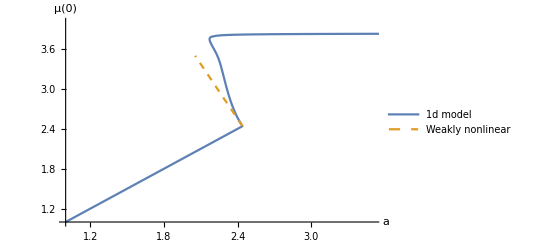

```mathematica
ListPlot[{Join[dataAmp[[1;;29]],dataAmp2[[1;;37]]],dataAmpw},Joined->True,PlotStyle->{{Full},{Dashed}},AxesLabel->{HoldForm[a],HoldForm[λ[A]-λ[0]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.5}],PlotRange->{{2.1,3.5},{0,0.16}}](*Figure 2(a) in the paper*)
dataμ0hom=Table[{x,x},{x,1,μcr,(μcr-1)/100}];
ListPlot[{Join[dataμ0hom,dataμ0[[1;;29]],dataμ02[[1;;37]]],dataμ0w},Joined->True,PlotStyle->{Full,Dashed},AxesLabel->{HoldForm[a],HoldForm[μ[0]]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},PlotLegends->Placed[LineLegend[{"1d model","Weakly nonlinear"},LegendMarkerSize->{30,5}, LegendLayout->{"Column",1}],{0.72,0.2}],PlotRange->{{1,3.5},{1,4}}] (*Figure 2(b) in the paper*)
```

#### 8. Evolution of axisymmetric necking given by the 1d model

{2.3996,2.29789,2.21108,2.17259,2.23,2.39}

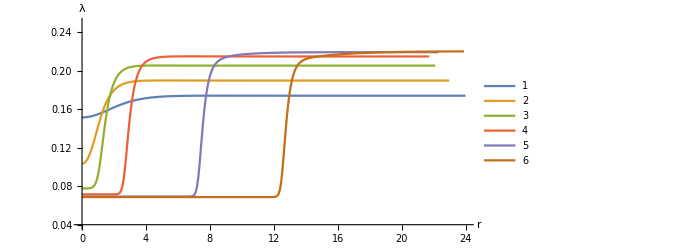

```mathematica
sollist={datasol[[3]],datasol[[12]],datasol[[20]],datasol[[23]],datasol2[[2]],datasol2[[6]]};(*solutions used to display the nekcing evolution*)
Table[μ[n]/.sollist[[i]],{i,1,Length[sollist]}](* corresponding value of a=μ[A]*)
Table[μevo[R_,i]=Piecewise[Table[{((h+h j-R) μ[j]+(-h j+R) μ[1+j])/h/.sollist[[i]],j h<=R<(j+1)h},{j,0,n-1}]],{i,1,Length[sollist]}];
Table[λevo[R_,i]=Piecewise[Table[{((h+h j-R) λ[j]+(-h j+R) λ[1+j])/h/.sollist[[i]],j h<=R<(j+1)h},{j,0,n-1}]],{i,1,Length[sollist]}];
ParametricPlot[Table[{μevo[R,i]*R,λevo[R,i]},{i,1,Length[sollist]}]//Evaluate,{R,0,A-0.01h},PlotLegends->Automatic,AxesLabel->{HoldForm[r],HoldForm[λ]},LabelStyle->{12,GrayLevel[0]},AxesStyle->{Directive[Black,Thickness[0.0035]],Directive[Black,Thickness[0.0035]]},AspectRatio->1/2,PlotRange->{{0,24},{0.04,0.25}},ImageSize->500](*Figure 4 in the paper*)
```

```mathematica
endtime= DateList[]
```

{2024,12,1,10,34,39.77733}

```mathematica
minutes=endtime[[5]]-starttime[[5]];
seconds=endtime[[6]]-starttime[[6]] ;
If[seconds<0, (seconds=(seconds+60))&&(minutes=minutes-1)];
Print["total run time =", minutes, " minutes +  ",seconds," seconds"]
```

total run time =10 minutes +  19.88419 seconds